```mathematica
(*Zerfallsrate von Z_c in Abhängigkeit der Photonmasse dm bei ϵ = 500keV und Λ = 500 MeV*)
```

```mathematica
Clear["Global`*"]
```

```mathematica
(*Welche Datei soll geladen werden?*)
FileEps=500;
FileLam=500;
string0=StringJoin["Gamma_eps",ToString[FileEps],"keV_lam",ToString[FileLam],"MeV.dat"]
plotlabel0=StringJoin["ϵ=",ToString[N[FileEps/1000]]," MeV\nΛ=",ToString[FileLam]," MeV"]
FileEps=5000;
FileLam=500;
string1=StringJoin["Gamma_eps",ToString[FileEps],"keV_lam",ToString[FileLam],"MeV.dat"]
plotlabel1=StringJoin["ϵ=",ToString[N[FileEps/1000]]," MeV\nΛ=",ToString[FileLam]," MeV"]
FileEps=500;
FileLam=800;
string2=StringJoin["Gamma_eps",ToString[FileEps],"keV_lam",ToString[FileLam],"MeV.dat"]
plotlabel2=StringJoin["ϵ=",ToString[N[FileEps/1000]]," MeV\nΛ=",ToString[FileLam]," MeV"]
FileEps=3000;
FileLam=650;
string3=StringJoin["Gamma_eps",ToString[FileEps],"keV_lam",ToString[FileLam],"MeV.dat"]
plotlabel3=StringJoin["ϵ=",ToString[N[FileEps/1000]]," MeV\nΛ=",ToString[FileLam]," MeV"]
FileEps=5000;
FileLam=800;
string4=StringJoin["Gamma_eps",ToString[FileEps],"keV_lam",ToString[FileLam],"MeV.dat"]
plotlabel4=StringJoin["ϵ=",ToString[N[FileEps/1000]]," MeV\nΛ=",ToString[FileLam]," MeV"]
```

Gamma_eps500keV_lam500MeV.dat

ϵ=0.5 MeV
Λ=500 MeV

Gamma_eps5000keV_lam500MeV.dat

ϵ=5. MeV
Λ=500 MeV

Gamma_eps500keV_lam800MeV.dat

ϵ=0.5 MeV
Λ=800 MeV

Gamma_eps3000keV_lam650MeV.dat

ϵ=3. MeV
Λ=650 MeV

Gamma_eps5000keV_lam800MeV.dat

ϵ=5. MeV
Λ=800 MeV

```mathematica
imgSize=500;
```

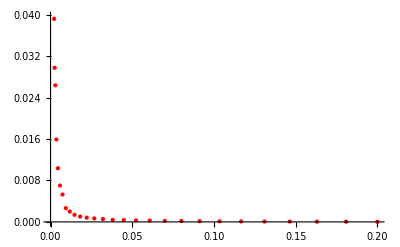
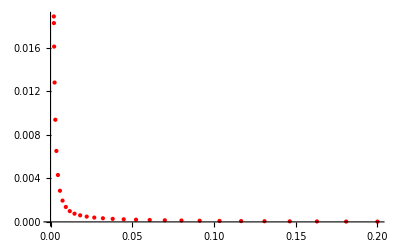
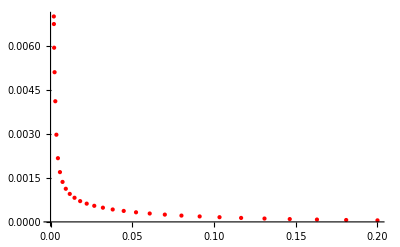
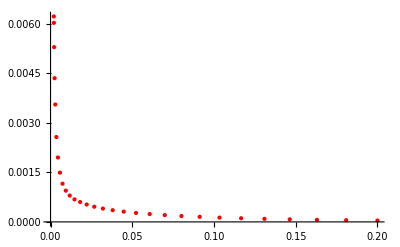
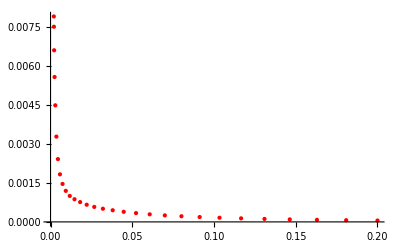

```mathematica
(*Datenwerte Laden, Duplikate aussortieren und fehlerhafte Einträge ignorieren*)
Gdm0=DeleteDuplicates[Delete[Cases[
Import[ToFileName[NotebookDirectory[],string0],"Table"],{_?NumberQ,_?NumberQ}],1]];
Gdm1=DeleteDuplicates[Delete[Cases[
Import[ToFileName[NotebookDirectory[],string1],"Table"],{_?NumberQ,_?NumberQ}],1]];
Gdm2=DeleteDuplicates[Delete[Cases[
Import[ToFileName[NotebookDirectory[],string2],"Table"],{_?NumberQ,_?NumberQ}],1]];
Gdm3=DeleteDuplicates[Delete[Cases[
Import[ToFileName[NotebookDirectory[],string3],"Table"],{_?NumberQ,_?NumberQ}],1]];
Gdm4=DeleteDuplicates[Delete[Cases[
Import[ToFileName[NotebookDirectory[],string4],"Table"],{_?NumberQ,_?NumberQ}],1]];
Row[{ListPlot[Gdm0[[All]],PlotStyle->Directive[PointSize[Medium],Red]],ListPlot[Gdm1[[All]],PlotStyle->Directive[PointSize[Medium],Red]],ListPlot[Gdm2[[All]],PlotStyle->Directive[PointSize[Medium],Red]],ListPlot[Gdm3[[All]],PlotStyle->Directive[PointSize[Medium],Red]],ListPlot[Gdm4[[All]],PlotStyle->Directive[PointSize[Medium],Red]]}]
```

```mathematica
g0=Gdm0[[All, {1, 2}]] 1000
g1=Gdm1[[All, {1, 2}]] 1000
g2=Gdm2[[All, {1, 2}]] 1000
g3=Gdm3[[All, {1, 2}]] 1000
g4=Gdm4[[All, {1, 2}]] 1000
```

{{2.00733,59.7778},{2.05867,47.0273},{2.198,39.1824},{2.46933,29.7437},{2.91667,26.354},{3.584,15.9123},{4.51533,10.35},{5.75467,7.00877},{7.346,5.28519},{9.33333,2.65591},{11.7607,1.99928},{14.672,1.3618},{18.1113,1.02942},{22.1227,0.821598},{26.75,0.673827},{32.0373,0.551795},{38.0287,0.389762},{44.768,0.351736},{52.2993,0.271703},{60.6667,0.239968},{69.914,0.189843},{80.0853,0.162794},{91.2247,0.135742},{103.376,0.112032},{116.583,0.0903335},{130.891,0.073694},{146.342,0.0587445},{162.981,0.0477926},{180.853,0.0374746},{200.,0.0297088}}

{{2.00733,18.8868},{2.05867,18.2758},{2.198,16.1172},{2.46933,12.8116},{2.91667,9.39158},{3.584,6.52314},{4.51533,4.31127},{5.75467,2.86385},{7.346,1.95772},{9.33333,1.37344},{11.7607,0.988779},{14.672,0.755774},{18.1113,0.603754},{22.1227,0.486875},{26.75,0.397999},{32.0373,0.334076},{38.0287,0.279908},{44.768,0.239357},{52.2993,0.2043},{60.6667,0.174281},{69.914,0.149462},{80.0853,0.126269},{91.2247,0.106847},{103.376,0.0896454},{116.583,0.0755827},{130.891,0.0627914},{146.342,0.0516838},{162.981,0.04236},{180.853,0.0342806},{200.,0.027583}}

{{2.00733,7.00638},{2.05867,6.74784},{2.198,5.9407},{2.46933,5.10515},{2.91667,4.11465},{3.584,2.97359},{4.51533,2.17274},{5.75467,1.69769},{7.346,1.36361},{9.33333,1.12998},{11.7607,0.954515},{14.672,0.822956},{18.1113,0.708598},{22.1227,0.622628},{26.75,0.548767},{32.0373,0.484694},{38.0287,0.423664},{44.768,0.374154},{52.2993,0.327308},{60.6667,0.286362},{69.914,0.24884},{80.0853,0.215376},{91.2247,0.186455},{103.376,0.16},{116.583,0.135621},{130.891,0.114708},{146.342,0.0960198},{162.981,0.0796477},{180.853,0.0645903},{200.,0.0522894}}

{{2.00733,6.22581},{2.05867,6.03179},{2.198,5.296},{2.46933,4.35448},{2.91667,3.55767},{3.584,2.5712},{4.51533,1.95199},{5.75467,1.49278},{7.346,1.15729},{9.33333,0.94717},{11.7607,0.797459},{14.672,0.682088},{18.1113,0.600952},{22.1227,0.527032},{26.75,0.459653},{32.0373,0.404143},{38.0287,0.354412},{44.768,0.310997},{52.2993,0.271532},{60.6667,0.237282},{69.914,0.205911},{80.0853,0.177446},{91.2247,0.152989},{103.376,0.130254},{116.583,0.110902},{130.891,0.0926949},{146.342,0.0769447},{162.981,0.0633817},{180.853,0.0512922},{200.,0.0408272}}

{{2.00733,7.92421},{2.05867,7.52791},{2.198,6.61948},{2.46933,5.58828},{2.91667,4.49691},{3.584,3.28967},{4.51533,2.42176},{5.75467,1.83449},{7.346,1.46447},{9.33333,1.19681},{11.7607,1.00126},{14.672,0.874001},{18.1113,0.764213},{22.1227,0.662765},{26.75,0.578257},{32.0373,0.507952},{38.0287,0.449432},{44.768,0.389493},{52.2993,0.339058},{60.6667,0.292811},{69.914,0.251726},{80.0853,0.21751},{91.2247,0.187167},{103.376,0.160671},{116.583,0.13683},{130.891,0.115045},{146.342,0.0960395},{162.981,0.0796498},{180.853,0.065087},{200.,0.0525025}}

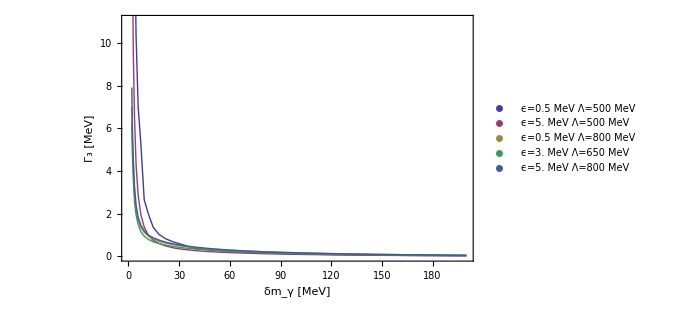

```mathematica
ListPlot[{g0,g1,g2,g3,g4},Joined->True,FrameLabel->{"δm_γ [MeV]","Γ_3 [MeV]"},Frame->True,PlotLegends->{Text[Style[plotlabel0,FontSize->11]],Text[Style[plotlabel1,FontSize->11]],Text[Style[plotlabel2,FontSize->11]],Text[Style[plotlabel3,FontSize->11]],Text[Style[plotlabel4,FontSize->11]]},LabelStyle->{FontSize->11},ImageSize->imgSize]
```

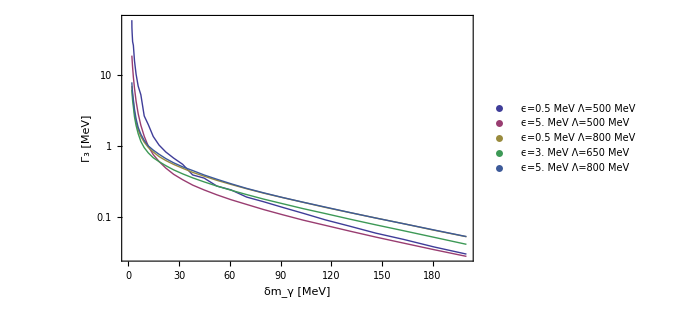

```mathematica
ListLogPlot[{g0,g1,g2,g3,g4},Joined->True,FrameLabel->{"δm_γ [MeV]","Γ_3 [MeV]"},Frame->True,PlotLegends->{Text[Style[plotlabel0,FontSize->11]],Text[Style[plotlabel1,FontSize->11]],Text[Style[plotlabel2,FontSize->11]],Text[Style[plotlabel3,FontSize->11]],Text[Style[plotlabel4,FontSize->11]]},LabelStyle->{FontSize->11},ImageSize->imgSize]
```

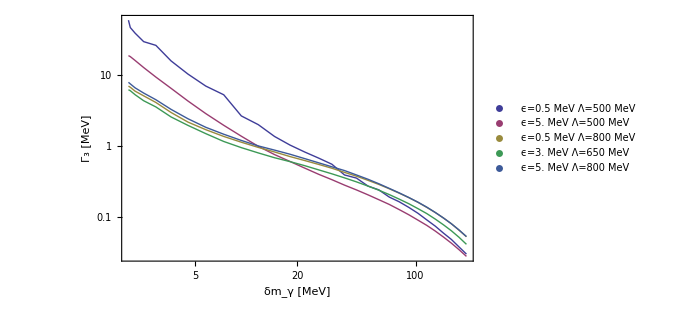

```mathematica
output=ListLogLogPlot[{g0,g1,g2,g3,g4},Joined->True,FrameLabel->{"δm_γ [MeV]","Γ_3 [MeV]"},Frame->True,PlotLegends->{Text[Style[plotlabel0,FontSize->11]],Text[Style[plotlabel1,FontSize->11]],Text[Style[plotlabel2,FontSize->11]],Text[Style[plotlabel3,FontSize->11]],Text[Style[plotlabel4,FontSize->11]]},LabelStyle->{FontSize->11},ImageSize->imgSize]
```

```mathematica
ig0=Interpolation[g0,InterpolationOrder->1]
ig1=Interpolation[g1,InterpolationOrder->1]
ig2=Interpolation[g2,InterpolationOrder->1]
ig3=Interpolation[g3,InterpolationOrder->1]
ig4=Interpolation[g4,InterpolationOrder->1]
```

InterpolatingFunction[{{2.00733,200.}},<>]

InterpolatingFunction[{{2.00733,200.}},<>]

InterpolatingFunction[{{2.00733,200.}},<>]

«2 more identical outputs»

```mathematica
model=(c1)/(c2+c3 dm+c4 dm^2);
fit0=FindFit[g0,model,{c1,c2,c3,c4},dm];
fg0[dm_]=model/.fit0
fit1=FindFit[g1,model,{c1,c2,c3,c4,c5},dm];
fg1[dm_]=model/.fit1
fit2=FindFit[g2,model,{c1,c2,c3,c4,c5},dm];
fg2[dm_]=model/.fit2
fit3=FindFit[g3,model,{c1,c2,c3,c4,c5},dm];
fg3[dm_]=model/.fit3
fit4=FindFit[g4,model,{c1,c2,c3,c4,c5},dm];
fg4[dm_]=model/.fit4
```

561.051/(-21.5782+14.9676 dm+0.422704 dm^2)

118.467/(-4.17516+3.87297 dm+0.642878 dm^2)

13.588/(-1.14214+1.55361 dm-0.00545295 dm^2)

18.6912/(-2.05099+2.54316 dm-0.00883351 dm^2)

13.8138/(-1.19413+1.48624 dm-0.00512364 dm^2)

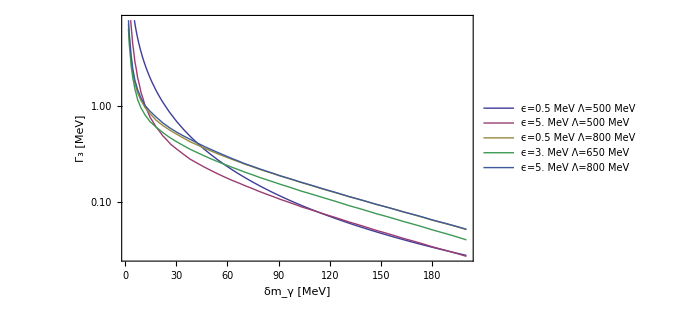

```mathematica
LogPlot[{fg0[dm],ig1[dm],ig2[dm],ig3[dm],ig4[dm]},{dm,2.00733,200},FrameLabel->{"δm_γ [MeV]","Γ_3 [MeV]"},Frame->True,PlotLegends->{Text[Style[plotlabel0,FontSize->11]],Text[Style[plotlabel1,FontSize->11]],Text[Style[plotlabel2,FontSize->11]],Text[Style[plotlabel3,FontSize->11]],Text[Style[plotlabel4,FontSize->11]]},LabelStyle->{FontSize->11},ImageSize->imgSize]
```

```mathematica
pmax[dm_]:=Piecewise[{{fg0[dm],fg0[dm]≥ig4[dm]},{ig4[dm],fg0[dm]≤ig4[dm]}}]
pmin[dm_]:=Piecewise[{{ig3[dm],ig1[dm]≥ig3[dm]},{ig1[dm],fg1[dm]≤ig3[dm]}}]
```

```mathematica
model=c4+(c1+c6 dm)/(c2+c3 dm+c5 dm^2+0c8 dm^3);
fitmax=FindFit[Table[{dm,pmax[dm]},{dm,2.00733,200,10}],model,{c1,c2,c3,c4,c5,c6,c7,c8},dm];
fmax[dm_]=model/.fitmax
```

-0.00748479+(-121051.-5887.27 dm)/(1852.37-1270.49 dm-424.439 dm^2)

```mathematica
imin=Interpolation[Table[{dm,pmin[dm]},{dm,2.00733,200,0.5}],InterpolationOrder->1]
```

InterpolatingFunction[{{2.00733,199.507}},<>]

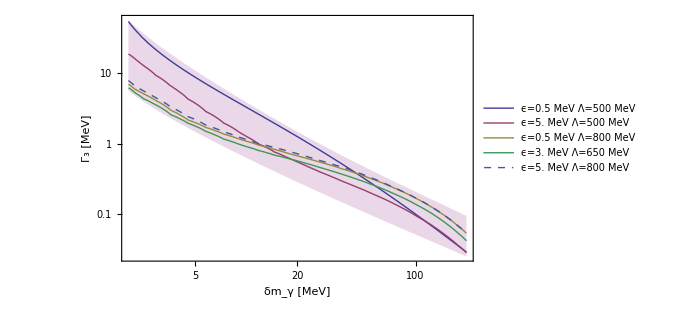

```mathematica
output=LogLogPlot[{fg0[dm],ig1[dm],ig2[dm],ig3[dm],ig4[dm],fmax[dm]+5/dm,(fmax[dm]+60/dm)/15},{dm,2.00733,200},FrameLabel->{"δm_γ [MeV]","Γ_3 [MeV]"},Frame->True,PlotLegends->{Text[Style[plotlabel0,FontSize->11]],Text[Style[plotlabel1,FontSize->11]],Text[Style[plotlabel2,FontSize->11]],Text[Style[plotlabel3,FontSize->11]],Text[Style[plotlabel4,FontSize->11]]},LabelStyle->{FontSize->11},ImageSize->imgSize,(*Filling->{1->{{4},Directive[Opacity[0.1],Blue]},2->{{5},Directive[Opacity[0.1],Blue]}},*)Filling->{6->{7}},PlotStyle->{Automatic,Automatic,Automatic,Automatic,Dashed,None,None}]
```

```mathematica
output=LogLogPlot[{
fg0[dm],
ig1[dm],
ig2[dm],
ig3[dm],
fmax[dm]+2/dm,
(fmax[dm]+70/dm)/15},{dm,2.00733,200},
FrameLabel->{"δ m_γ [MeV]","Γ_3 [MeV]"},
Frame->True,
PlotLegends->Placed[
LineLegend[
{Text[Style[plotlabel0,FontSize->13]],
Text[Style[plotlabel1,FontSize->13]],
Text[Style[plotlabel2,FontSize->13]],
Text[Style[plotlabel3,FontSize->13]]},
LegendLayout->{"Row",1}],{Above,Top}],
LabelStyle->{FontSize->18},
ImageSize->imgSize,
Filling->{5->{{6},Directive[Opacity[0.15],Purple]}},
PlotStyle->{Automatic,Automatic,Automatic,Automatic,None,None}]
```

-Graphics-

```mathematica
Export["GammaMgam.eps",output,ImageResolution->400]
```

GammaMgam.eps